```mathematica
SetDirectory[NotebookDirectory[]];
curve1=Import["../cmake-build-debug-mingw/curve1.csv"];
curve2=Import["../cmake-build-debug-mingw/curve2.csv"];
matching=Import["../cmake-build-debug-mingw/matching.csv"];
```

```mathematica
(* Interpolating Line objects: *)
ClearAll[LineInterpolation,LineBreakPoints];

Options[LineBreakPoints]={Normalize->False};
LineBreakPoints[line_,opts:OptionsPattern[]]:=(
accum=Accumulate[#]&@Prepend[Norm[Subtract@@#]&/@Partition[line[[1]],2,1],0];
If[OptionValue[Normalize],accum/ArcLength[line],accum]);

LineInterpolation[line_,opts:OptionsPattern[{LineBreakPoints,Interpolation}]]:=(
breakpoints=LineBreakPoints[line,Sequence@@FilterRules[{opts},Options[LineBreakPoints]]];
Interpolation[Transpose[{breakpoints,line[[1]]}],InterpolationOrder->1,Sequence@@FilterRules[{opts},Options[Interpolation]]]);
```

```mathematica
c1=LineInterpolation[Line[curve1]];
c2=LineInterpolation[Line[curve2]];
m=LineInterpolation[Line[matching],Normalize->True];
```

```mathematica
len1=ArcLength@Line[curve1];
len2=ArcLength@Line[curve2];
```

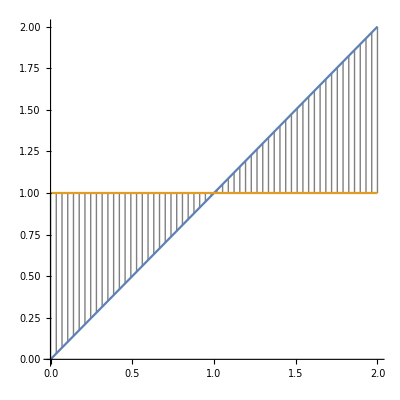

```mathematica
Show[
ListLinePlot[
Table[Quiet@({c1[#1],c2[#2]}&@@m[t]),{t,0,1,1/Ceiling[20 Max[len1,len2]]}],
PlotStyle->Directive[Gray,Thin]
],
ParametricPlot[{c1[t len1],c2[t len2]},{t,0,1}],
AspectRatio->Automatic
]
```

```mathematica
Clear[Dist];
Dist[t1_,t2_]=Norm[c1[t1]-c2[t2],2];
NIntegrate[(Dist[m[t][[1]],m[t][[2]]])*Norm[m'[t],Infinity],{t,0,1}]
```

Part::partw: Part 2 of InterpolatingFunction[{{0.,1.}},{5,3,0,{3},{2},0,0,0,0,Automatic,{},{},False},{{0.,0.5,1.}},{{{0.,0.}},{{1.41421,1.}},{{2.82843,2.}}},{Automatic}][t] does not exist.

2.82914